```mathematica
directPower[theta_, day_] := ( (* angle with sun, day of year *)
i= 1367 (1+0.034 Cos[360*day/365.25]);
aZero = 0.2538 - 0.0063 36;
aOne = 0.7678 + 0.001 6.5^2;
k = 0.249 + 0.081 2.5^2;
If[Cos[theta]<0,
0, (* If the sun is more than 90 degrees off, the formula is not correct, and we set the insolation to 0 *)
i (aZero + aOne E^(-k/Cos[theta])) 
] 
);
directPower[0.5, 10] // N
directPower[0.34, 253] // N
directPower[0, 0] // N
directPower[3.14, 10] // N
```

489.607

526.962

576.186

0.

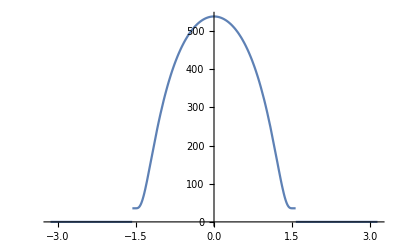

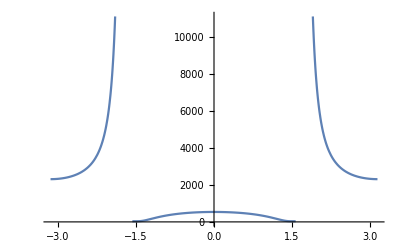

```mathematica
Plot[directPower[theta, 150], {theta, -Pi,Pi}]
directPower2[theta_, day_] := ( (* angle with sun, day of year *)
i= 1367 (1+0.034 Cos[360*day/365.25]);
aZero = 0.2538 - 0.0063 36;
aOne = 0.7678 + 0.001 6.5^2;
k = 0.249 + 0.081 2.5^2;
i (aZero + aOne E^(-k/Cos[theta])) 
);
Plot[directPower2[theta, 150], {theta, -Pi,Pi }]
```

```mathematica
position = GeoPosition[{51.546545,4.411744}];

DateObject[{2018, 7, 30, 10, 29, 0}] (* correct, this is GMT+2 *)
DateObject[{2018, 7, 30, 10, 29, 0}, TimeZone -> "Europe/Amsterdam" ] (* correct, CEST is now GMT+2 *)
DateObject[{2019, 1, 1, 6, 0, 0}] (* incorrect, this is GMT+2 *)
DateObject[{2019, 1, 1, 6, 0, 0}, TimeZone -> "Europe/Amsterdam" ] (* correct, CEST is now GMT+1 *)

SunPosition[position, DateObject[{2018, 7, 30, 10, 29, 0}]]
SunPosition[position, DateObject[{2018, 7, 30, 10, 29, 0}, TimeZone -> "Europe/Amsterdam" ]]
SunPosition[position, DateObject[{2019, 1, 1, 6, 0, 0} ]]
SunPosition[position, DateObject[{2019, 1, 1, 6, 0, 0}, TimeZone -> "Europe/Amsterdam" ]]
AbsoluteTiming[SunPosition[position, DateObject[{2019, 1, 1, 12, 0, 0}, TimeZone -> "Europe/Amsterdam"]]]
(* { azimuth, altitude } *)
```

Mon 30 Jul 2018 10:29:00GMT+2.

Mon 30 Jul 2018 10:29:00CEST

Tue 1 Jan 2019 06:00:00GMT+2.

Tue 1 Jan 2019 06:00:00CEST

{111.15 °,38.89 °}

{111.15 °,38.89 °}

{84.65 °,-34.11 °}

{96.37 °,-24.8 °}

{0.0227358,{169.12 °,14.77 °}}

```mathematica
sunMisalignment[sunPos_,a_]:= ( (* angle[sun position, solar panel angle in degrees] returns misalignment with the sun (zenith) in radians *)
(* remove degree unit, then convert to radians *)
gammaS= QuantityMagnitude[Quantity[sunPos[[1]]]]*Pi/180;  (* Azimuth of sun position, 0 due South, negative to the east *)
(* Because Mathematica gives azimuth in compass angle, we subtract 180 degrees *)
gammaS = gammaS - Pi;
thetaS= QuantityMagnitude[Quantity[sunPos[[2]]]]*Pi/180; (* Sun altitude *)
gammaP = -22 * Pi/180; (* Solar panels azimuth *)
thetaP = a * Pi/180; (* Solar panels angle with horizontal *)
ArcCos[Cos[gammaP-gammaS] Cos[thetaS] Sin[thetaP]+Cos[thetaP] Sin[thetaS]] (* The formula to find the zenith, see docs *)
)
position = GeoPosition[{51.546545,4.411744}];
sunPos = SunPosition[position, DateObject[{2018, 8, 1, 15, 57, 0}, TimeZone -> "Europe/Amsterdam"]];
sunMisalignment[sunPos, 42]

sunPos = SunPosition[position, DateObject[{2020, 11, 24, 17, 15, 0}, TimeZone -> "Europe/Amsterdam"]];
sunMisalignment[sunPos, 60]
```

0.7983

1.541

```mathematica
SunRise[position, DateObject[{2018, 7, 30, 10, 29, 0}, TimeZone -> "Europe/Amsterdam"]]; (* idk *)
```

```mathematica
totalPower[sunPositions_,alpha_,day_]:=(Sum[directPower[sunMisalignment[sunPos,alpha],day],{sunPos,sunPositions}]);
position=GeoPosition[{51.546545,4.411744}];
pos1=SunPosition[position,DateObject[{2018,8,1,18,35,0}, TimeZone -> "Europe/Amsterdam"]];
pos2=SunPosition[position,DateObject[{2018,3,3,16,35,0}, TimeZone -> "Europe/Amsterdam"]];
totalPower[{pos1,pos2},24,145]

pos1=SunPosition[position,DateObject[{2018,2,1,20,35,0}, TimeZone -> "Europe/Amsterdam"]];
pos2=SunPosition[position,DateObject[{2018,3,17,12,0,0}, TimeZone -> "Europe/Amsterdam"]];
pos3=SunPosition[position,DateObject[{2018,3,17,12,10,0}, TimeZone -> "Europe/Amsterdam"]];
totalPower[{pos1,pos2,pos3},5,2]

pos1=SunPosition[position,DateObject[{2018,8,1,19,00,0}, TimeZone -> "Europe/Amsterdam"]];
pos2=SunPosition[position,DateObject[{2018,8,1,19,10,0}, TimeZone -> "Europe/Amsterdam"]];
pos3=SunPosition[position,DateObject[{2018,8,1,19,16,0}, TimeZone -> "Europe/Amsterdam"]];
pos4=SunPosition[position,DateObject[{2018,8,1,19,18,0}, TimeZone -> "Europe/Amsterdam"]];
totalPower[{pos1,pos2,pos3,pos4},0,212]
QuantityMagnitude[Quantity[DateObject[{2018,8,1}]-DateObject[{2018,1,1}]]]
```

237.324

767.742

619.392

212